## Without Piecewise notation

```mathematica
g=x-1;
{a,b}={1,3};
A=Integrate[g,{x,a,b}]
k=1/A
f=k g//Expand
 Integrate[f,{x,a,b}]==1
EV = Integrate[x f,{x,a,b}]
Var=Integrate[(x-EV)^2f,{x,a,b}]
Integrate[f,{x,1.5,2.6}]
F=Integrate[f,{x,a,x}]
D[F,x]
```

2

1/2

-1/2+x/2

True

7/3

2/9

0.5775

(1-x)/2+1/2 (-1/2+x^2/2)

-1/2+x/2

## Using Piecewise Notation

```mathematica
g=Piecewise[{
{x-1,1<=x<=3},
{0,True}
}]
```

Piecewise[{{-1+x, 1≤x≤3}, {0, True}}]

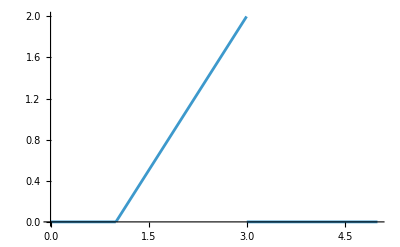

```mathematica
Plot[g,{x,0,5}]
```

```mathematica
{a,b}={-Infinity,Infinity}
A=Integrate[g,{x,a,b}]
k=1/A
f=k g
EV = Integrate[x f,{x,a,b}]
Var= Integrate[(x-EV)^2 f,{x,a,b}]
```

{-∞,∞}

2

1/2

1/2 (Piecewise[{{-1+x, 1≤x≤3}, {0, True}}])

7/3

2/9

```mathematica
Integrate[f,{x,1.5,2.6}]
F=Integrate[f,{x,a,x}]
D[F,x]
```

0.5775

Integrate::pwrl: Unable to prove that integration limits {x} are real. Adding assumptions may help.

∫_(-∞)^x 1/2 (Piecewise[{{-1+x, 1≤x≤3}, {0, True}}])ⅆx

∂_x ∫_(-∞)^x 1/2 (Piecewise[{{-1+x, 1≤x≤3}, {0, True}}])ⅆx

## Homework Practice

```mathematica
g=x^2+x;
{a,b}={0,1};
A=Integrate[g,{x,a,b}];
k=1/A
```

6/5

1

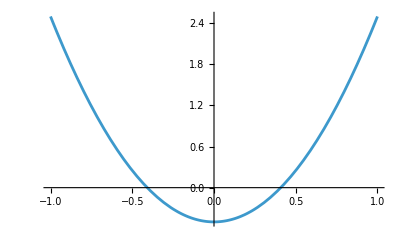

```mathematica
g=3x^2-1/2;
{a,b}={-1,1};
A=Integrate[g,{x,a,b}];
k=1/A
Plot[g,{x,a,b}]
```

```mathematica
g=Piecewise[{
{1/4,0<=x<=2},
{1/4(2x-3),2<=x<=3},
{0,True}
}];
Integrate[g,{x,0,3}]
```

Piecewise[{{1/4, 0≤x≤2}, {1/4 (-3+2 x), 2≤x≤3}, {0, True}}]

1

```mathematica
Integrate[g,{x,0,2.5}]
Integrate[g,{x,-Infinity,2.5}]
```

0.6875

0.6875

## Method of Moments Introduction

```mathematica
$Assumptions=σ>0;
f=1/Sqrt[2*π*σ^2] Exp[-1/2*((x-μ)/σ)^2];
bounds={x,-Infinity,Infinity};
EV=Integrate[x f,bounds]
Var=Integrate[(x-EV)^2 f,bounds]
$Assumptions=Null
```

μ

σ^2

```mathematica
$Assumptions=α>0&&β>0;
f=(β^α/Gamma[α]) x^(α-1) Exp[-β*x];
bounds={x,0,Infinity};
EV=Integrate[x f,bounds]
Var=Integrate[(x-EV)^2 f,bounds]
$Assumptions=Null
```

α/β

α/β^2

```mathematica
Solve[{α/β==mean,α/β^2==var},{α,β}]
```

{{α→mean^2/var,β→mean/var}}